# Problem 1

```mathematica
params=<|
upstream-> LinguisticAssistant,
flow1-> 27.2*Quantity[1000000, ("Gallons")/("Days")],
flow2->12*Quantity[1000000, ("Gallons")/("Days")],
conc0 -> 100/Quantity[100, "Milliliters"],
conc1->200/Quantity[100, "Milliliters"],
conc2->1000/Quantity[100, "Milliliters"]
|>;
flow12=upstream + flow1;
flow123=flow12+flow2;
(*flow12=flow123=upstream;*)
```

```mathematica
sys1=upstream * conc0 + flow1 * conc1 - conc12 * flow12 == 0;
sys2=conc12 * flow12+conc2*flow2-conc123*flow123 == 0;
```

```mathematica
sol=Solve[{sys1, sys2}, {conc12, conc123}][[1]]
```

{conc12→-(-conc1 flow1-conc0 upstream)/(flow1+upstream),conc123→-(-conc1 flow1-conc2 flow2-conc0 upstream)/(flow1+flow2+upstream)}

```mathematica
UnitConvert[{flow12,flow123}/.params,"L/s"]
UnitConvert[sol/.params]
```

{29508.6 L/s,30034.3 L/s}

{conc12→1.04039×10^6 per meter^3,conc123→1.19722×10^6 per meter^3}

# Problem 2

```mathematica
time=LinguisticAssistant;
```

```mathematica
params=<|
upstream-> LinguisticAssistant,
flow1-> 27.2*Quantity[1000000, ("Gallons")/("Days")],
flow2->12*Quantity[1000000, ("Gallons")/("Days")],
conc0 -> 100/Quantity[100, "Milliliters"],
conc1->200/Quantity[100, "Milliliters"],
conc2->1000/Quantity[100, "Milliliters"],
k->-0.03/Quantity[, "Days"]
|>;
flow12=upstream + flow1;
flow123=flow12+flow2;
(*flow12=flow123=upstream;*)
```

```mathematica
sys1=upstream * conc0 + flow1 * conc1 - cmid[0] * flow12 == 0;
sys2=cmid[time] * flow12+conc2*flow2-conc123*flow123 == 0;
decay=cmid'[t]==cmid[t]*k;
```

```mathematica
sol=DSolve[{decay,sys1}, cmid[t],t][[1]]
```

{cmid[t]→(ⅇ^(k t) (conc1 flow1+conc0 upstream))/(flow1+upstream)}

```mathematica
cmid/.params
```

cmid

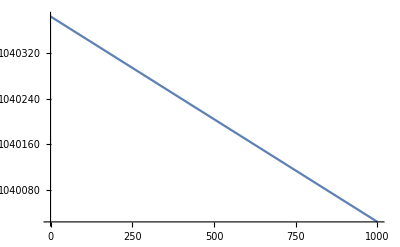

```mathematica
Plot[Evaluate[cmid[t]/.sol/.params],{t,Quantity[0, "Days"],LinguisticAssistant}]
```

```mathematica
Solve[{sys1,sys2}/.(cmid[t_]:>(ⅇ^(k t) (conc1 flow1+conc0 upstream))/(flow1+upstream)),conc123]/.params
```

{{conc123→1.16701 /mL}}

```mathematica
UnitConvert[{flow12,flow123}/.params,"L/s"]
UnitConvert[sol/.params]
```

{29508.6 L/s,30034.3 L/s}

{cmid[t]→ⅇ^(t (-3.47222×10^-7 per second)) (1.04039×10^6 per meter^3)}